```mathematica
Clear["Global`*"]
```

```mathematica
r[t_] = {3Cos[3.3π*t], Sin[4π*t] + 4*t};
```

```mathematica
track =ParametricPlot[r[t], {t, 0, 1}, AxesLabel-> {Style["x", Bold], Style["y", Bold]}, PlotRange->All, ImageSize->Full];
```

Find the location of the Pont; where the course crosses itself.

```mathematica
bridge = t/.FindRoot[{r[t] == r[s]},{t,0}, {s, 0.5}] (* grab the t value found from FindRoot. s would work as well. *)
```

0.134804

```mathematica
cauchy = Graphics[Style[Disk[r[0], 0.06], Green]]; 
laplace = Graphics[Style[Disk[r[1], 0.06], Red]];
pont = Graphics[Style[Disk[r[bridge], 0.06], Orange]];
```

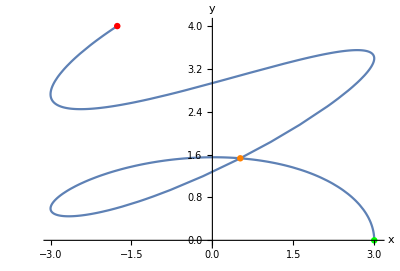

```mathematica
Show[track, cauchy, laplace, pont]
```

Speed is just the magnitude of the velocity vector at a given time, t.

```mathematica
v[t_] = r'[t];
```

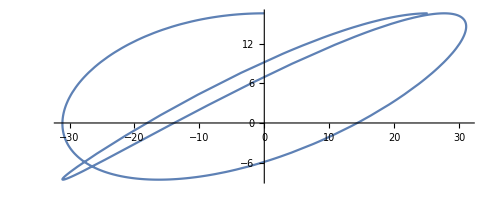

```mathematica
ParametricPlot[v[t], {t, 0, 1}]
```

The average speed is the distanced travelled (arc length 0->1) over the time it took (1hr).
Integrate the scalar magnitude of r[t] from t = 0->1 and devide by 1 hour.

```mathematica
NIntegrate[Norm[v[t]], {t, 0, 1}] (* 22.0332 km/hr *)
```

22.0332

Distance between Cauchy and Laplace. (3.)

```mathematica
dbt = EuclideanDistance[r[0],r[1]] (* 6.22009 km | dbt = distance between towns *)
```

6.22009

(4.)

```mathematica
ft[t_?NumericQ]:=NIntegrate[r[t],{t,0,x}]
```

```mathematica
FindRoot[ft[t] == 1, {x,0}]
```

FindRoot::nlnum: The function value {-1. + ft[t]} is not a list of numbers with dimensions {1} at {x} = {0.}.

FindRoot[ft[t]==1,{x,0}]

```mathematica
f[t_?NumericQ]:=NIntegrate[x^2,{x,0,t}];
FindRoot[f[t]==1,{t,1.2}]
```

{t→1.44225}

```mathematica
kmpt[t_?NumericQ] := NIntegrate[Norm[v[t]], {t, 0, s}];
FindRoot[kmpt[t] == 1, {t, 0}]
```

NIntegrate::itraw: Raw object 0. cannot be used as an iterator.

FindRoot::nlnum: The function value {-1. + NIntegrate[Norm[v[0.]], {0., 0., s}]} is not a list of numbers with dimensions {1} at {t} = {0.}.

FindRoot[kmpt[t]==1,{t,0}]

(5.)
Curvature = ||T’(t)|| / ||r’(t)||
T’(t) = r’(t) / ||r’(t)||, but r’(t) is v(t)

```mathematica
T[t_] = v[t]/Norm[v[t]];
K[t_] = Norm[T'[t]]/Norm[v[t]];
```

```mathematica
curvature = Plot[K[t], {t, 0, 1}];
Show[curvature]
```

-Graphics-